# THIS TAKES ABOUT 20 MINUTES TO RUN

### Create a state equation using MMS.

```mathematica
A=-{{1,0},{1,2}}
```

(-1 | 0
-1 | -2)

```mathematica
T=1/20{{{1,2},{3,4}}, {{1,1},{0,3}}}
```

({1/20,1/10} | {3/20,1/5}
{1/20,1/20} | {0,3/20})

Pick a “seed” function to generate the forcing function b(t). IMPORTANT: this will not (usually) be the solution to the optimization problem, because in the optimization setting we’re free to choose initial values to get a better fit to the target.

```mathematica
Subscript[x, seed][t_]={ (1/2+t^2)Exp[-t], (1/3+t) Exp[-2t] }
```

{ⅇ^-t (t^2+1/2),ⅇ^(-2 t) (t+1/3)}

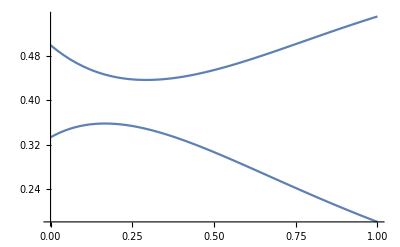

```mathematica
Plot[Subscript[x, seed][t],{t,0,1}]
```

Define the multiplication of a tensor by a vector

```mathematica
tensorVecProduct[t_,v_]:=Table[v.t[[i]].v,{i,1,Length[t]}]
```

Create the RHS function b(t)

```mathematica
b[t_]=Table[Subscript[x, seed]'[t][[i]] - Sum[A[[i,j]] Subscript[x, seed][t][[j]],{j,1,2}]
- Sum[T[[i,j,k]]Subscript[x, seed][t][[j]]Subscript[x, seed][t][[k]],{j,1,2},{k,1,2}],{i,1,2}]//FullSimplify
Subscript[x, seed]'[t]-A.Subscript[x, seed][t]-tensorVecProduct[T,Subscript[x, seed][t]];
b[t]==%//FullSimplify
```

{1/20 ⅇ^(-4 t) (-5 ⅇ^t (t^2+1/2) (t+1/3)-ⅇ^(2 t) (t^2+1/2)^2-4 (t+1/3)^2+40 ⅇ^(3 t) t),1/240 ⅇ^(-4 t) (-2 ⅇ^t (2 t^2+1) (3 t+1)+120 ⅇ^(3 t) (2 t^2+1)-3 ⅇ^(2 t) (4 (t^4+t^2)-79)-4 (3 t+1)^2)}

True

#### Use DSolve to produce the general solution to the ODE we’ve manufactured

```mathematica
X[t_]={Subscript[x, 1][t],Subscript[x, 2][t]}
```

{x_1(t),x_2(t)}

Solve using parameters α and β as the initial conditions.

```mathematica
stateEqn = Table[X'[t][[i]] - Sum[A[[i,j]] X[t][[j]],{j,1,2}]
- Sum[T[[i,j,k]]X[t][[j]]X[t][[k]],{j,1,2},{k,1,2}]-b[t][[i]],{i,1,2}]=={0,0}
 Table[X'[t][[i]] - Sum[A[[i,j]] X[t][[j]],{j,1,2}]
- Sum[T[[i,j,k]]X[t][[j]]X[t][[k]],{j,1,2},{k,1,2}]-b[t][[i]],{i,1,2}]==(X'[t]-A.X[t]-tensorVecProduct[T,X[t]]-b[t])//FullSimplify
```

{-1/20 ⅇ^(-4 t) (-5 ⅇ^t (t^2+1/2) (t+1/3)-ⅇ^(2 t) (t^2+1/2)^2-4 (t+1/3)^2+40 ⅇ^(3 t) t)+x_1'(t)-1/20 (x_1(t))^2-1/4 x_2(t) x_1(t)+x_1(t)-1/5 (x_2(t))^2,-1/240 ⅇ^(-4 t) (-2 ⅇ^t (2 t^2+1) (3 t+1)+120 ⅇ^(3 t) (2 t^2+1)-3 ⅇ^(2 t) (4 (t^4+t^2)-79)-4 (3 t+1)^2)+x_2'(t)-1/20 (x_1(t))^2-1/20 x_2(t) x_1(t)+x_1(t)-3/20 (x_2(t))^2+2 x_2(t)}=={0,0}

True

```mathematica
xSoln[α_,β_,t_]:=X[t]/.NDSolve[{stateEqn,X[0]=={α,β}},X[t],{t,0,1}][[1]]
```

Sanity check: make sure we recover the seed function when we use as ICs the initial value; x_seed[0]={1/2,1/3}

```mathematica
xSoln[1/2,1/3,t]/.t->0
```

{0.5,0.333333}

### Pick a target function

I’ll choose a target that’s a perturbation of the seed function, parametrized by γ. When γ=0 we get back the seed function.

```mathematica
SuperStar[x][γ_,t_]=Subscript[x, seed][t] + γ {t(t-1/2),(t-3/4)/5}
```

{ⅇ^-t (t^2+1/2)+γ (t-1/2) t,1/5 γ (t-3/4)+ⅇ^(-2 t) (t+1/3)}

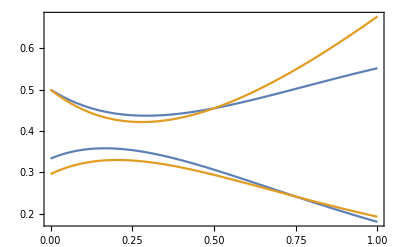

```mathematica
Plot[{Subscript[x, seed][t],SuperStar[x][1/4,t]},{t,0,1}]
```

### Set up the objective function

Integrand: square the difference between a solution to the ODE (given ICs α and β) and the target.

```mathematica
F[α_,β_,γ_,t_]:=(xSoln[α,β,t]-SuperStar[x][γ,t]).(xSoln[α,β,t]-SuperStar[x][γ,t])
```

Integrate to compute the objective function

```mathematica
f[α_,β_,γ_]:=1/2 NIntegrate[F[α,β,γ,t],{t,0,1}]
```

```mathematica
f[0.4,0.4,0.1]
```

0.00410607

```mathematica
gridVals[γ_] := Table[f[α,β,γ],{α,0,1,0.1},{β,0,1,0.1}]
```

```mathematica
ListPlot3D[gridVals[0.1],AxesLabel->Automatic]
```

-Graphics3D-

### Minimize

```mathematica
FindMinimum[f[α,β,0.2],{{α,0,1},{β,0,1}},Method->"PrincipalAxis"]
```

NDSolve::ndinnt: Initial condition α is not a number or a rectangular array of numbers.

ReplaceAll::reps: {{-1/20 ⅇ^(-4 t) (40 Power[«2»] t-4 Power[«2»]-5 Power[«2»] Plus[«2»] Plus[«2»]-Power[«2»] Power[«2»])+x_1(t)-1/20 (x_1(t))^2-1/4 x_1(t) x_2(t)-1/5 (x_2(t))^2+x_1'(t),-1/240 ⅇ^(«1») (-4 Power[«2»]+«5»)+«8»+«1»}==«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition α is not a number or a rectangular array of numbers.

ReplaceAll::reps: {{-1/20 ⅇ^(-4 t) (40 Power[«2»] t-4 Power[«2»]-5 Power[«2»] Plus[«2»] Plus[«2»]-Power[«2»] Power[«2»])+x_1(t)-1/20 (x_1(t))^2-1/4 x_1(t) x_2(t)-1/5 (x_2(t))^2+x_1'(t),-1/240 ⅇ^(«1») (-4 Power[«2»]+«5»)+«8»+«1»}==«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{-0.05 2.71828^(-4. t) (40. Power[«2»] t-4. Power[«2»]-5. Power[«2»] Plus[«2»] Plus[«2»]-1. Power[«2»] Power[«2»])+x_1(t)-0.05 («1»(t))^2-«1»-0.2 (x_2(t))^2+x_1'(t),«1»+«8»+«1»(t)}==«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.04 (-3/4+t)-«1»+({x_1(t),x_2(t)}/.{{Plus[«6»],Plus[«7»]}=={0,0},«1»=={«1»}}))^2+(«1»)^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1).

{0.000671333,{α→0.512925,β→0.31179}}

```mathematica
data=Table[{γ,FindMinimum[f[α,β,γ],{{α,0.2,0.6},{β,0.2,0.6}},Method->"PrincipalAxis"]},{γ,0,0.2,0.01}]
```

NDSolve::ndinnt: Initial condition α is not a number or a rectangular array of numbers.

ReplaceAll::reps: {{-1/20 ⅇ^(-4 t) (40 Power[«2»] t-4 Power[«2»]-5 Power[«2»] Plus[«2»] Plus[«2»]-Power[«2»] Power[«2»])+x_1(t)-1/20 (x_1(t))^2-1/4 x_1(t) x_2(t)-1/5 (x_2(t))^2+x_1'(t),-1/240 ⅇ^(«1») (-4 Power[«2»]+«5»)+«8»+«1»}==«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndinnt: Initial condition α is not a number or a rectangular array of numbers.

ReplaceAll::reps: {{-1/20 ⅇ^(-4 t) (40 Power[«2»] t-4 Power[«2»]-5 Power[«2»] Plus[«2»] Plus[«2»]-Power[«2»] Power[«2»])+x_1(t)-1/20 (x_1(t))^2-1/4 x_1(t) x_2(t)-1/5 (x_2(t))^2+x_1'(t),-1/240 ⅇ^(«1») (-4 Power[«2»]+«5»)+«8»+«1»}==«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{-0.05 2.71828^(-4. t) (40. Power[«2»] t-4. Power[«2»]-5. Power[«2»] Plus[«2»] Plus[«2»]-1. Power[«2»] Power[«2»])+x_1(t)-0.05 («1»(t))^2-«1»-0.2 (x_2(t))^2+x_1'(t),«1»+«8»+«1»(t)}==«1»,«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.-«1»+({x_1(t),x_2(t)}/.{{Plus[«6»],Plus[«7»]}=={0,0},{Subscript[«2»][«1»],«1»[«1»]}==«1»}))^2+(0.-«1»+({x_1(t),x_2(t)}/.{{«1»}=={0,0},«1»}))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1).

NDSolve::ndinnt: Initial condition α is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

NIntegrate::inumr: The integrand (-0.002 (-3/4+t)-«1»+({x_1(t),x_2(t)}/.{{Plus[«6»],Plus[«7»]}=={0,0},{«1»,«9»[«2»][«1»]}==«1»}))^2+(-0.01 (-1/2+t) t-ⅇ^-t (1/2+t^2)+(«1»))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1).

NIntegrate::inumr: The integrand (-0.004 (-3/4+t)-«1»+({x_1(t),x_2(t)}/.{{Plus[«6»],Plus[«7»]}=={0,0},{«1»,«9»[«2»][«1»]}==«1»}))^2+(-0.02 (-1/2+t) t-ⅇ^-t (1/2+t^2)+(«1»))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

(0. | {2.13097×10^-15,{α→0.5,β→0.333333}}
0.01 | {1.6786×10^-6,{α→0.500647,β→0.332259}}
0.02 | {6.71431×10^-6,{α→0.501294,β→0.331185}}
0.03 | {0.000015107,{α→0.501941,β→0.33011}}
0.04 | {0.0000268567,{α→0.502588,β→0.329035}}
0.05 | {0.0000419633,{α→0.503235,β→0.327959}}
0.06 | {0.0000604266,{α→0.503881,β→0.326884}}
0.07 | {0.0000822467,{α→0.504528,β→0.325808}}
0.08 | {0.000107423,{α→0.505175,β→0.324731}}
0.09 | {0.000135957,{α→0.505821,β→0.323655}}
0.1 | {0.000167846,{α→0.506467,β→0.322578}}
0.11 | {0.000203093,{α→0.507114,β→0.3215}}
0.12 | {0.000241695,{α→0.50776,β→0.320423}}
0.13 | {0.000283654,{α→0.508406,β→0.319345}}
0.14 | {0.000328968,{α→0.509052,β→0.318267}}
0.15 | {0.000377639,{α→0.509698,β→0.317188}}
0.16 | {0.000429666,{α→0.510343,β→0.316109}}
0.17 | {0.000485049,{α→0.510989,β→0.31503}}
0.18 | {0.000543788,{α→0.511635,β→0.31395}}
0.19 | {0.000605882,{α→0.51228,β→0.31287}}
0.2 | {0.000671333,{α→0.512925,β→0.31179}})

```mathematica
ab=Table[{data[[i,1]],α,β}/.data[[i,2,2]],{i,1,Length[data]}]
```

(0. | 0.5 | 0.333333
0.01 | 0.500647 | 0.332259
0.02 | 0.501294 | 0.331185
0.03 | 0.501941 | 0.33011
0.04 | 0.502588 | 0.329035
0.05 | 0.503235 | 0.327959
0.06 | 0.503881 | 0.326884
0.07 | 0.504528 | 0.325808
0.08 | 0.505175 | 0.324731
0.09 | 0.505821 | 0.323655
0.1 | 0.506467 | 0.322578
0.11 | 0.507114 | 0.3215
0.12 | 0.50776 | 0.320423
0.13 | 0.508406 | 0.319345
0.14 | 0.509052 | 0.318267
0.15 | 0.509698 | 0.317188
0.16 | 0.510343 | 0.316109
0.17 | 0.510989 | 0.31503
0.18 | 0.511635 | 0.31395
0.19 | 0.51228 | 0.31287
0.2 | 0.512925 | 0.31179)

```mathematica
aDat = ab[[;;,1;;2]]
```

(0. | 0.5
0.01 | 0.500647
0.02 | 0.501294
0.03 | 0.501941
0.04 | 0.502588
0.05 | 0.503235
0.06 | 0.503881
0.07 | 0.504528
0.08 | 0.505175
0.09 | 0.505821
0.1 | 0.506467
0.11 | 0.507114
0.12 | 0.50776
0.13 | 0.508406
0.14 | 0.509052
0.15 | 0.509698
0.16 | 0.510343
0.17 | 0.510989
0.18 | 0.511635
0.19 | 0.51228
0.2 | 0.512925)

```mathematica
aFit[γ_]=Fit[aDat, {1,γ,γ^2,γ^3},γ]
```

-0.000016134 γ^3-0.000449135 γ^2+0.0647176 γ+0.5

```mathematica
aFit[aDat[[;;,1]]]-aDat[[;;,2]]
```

{-7.31409×10^-10,-1.87382×10^-9,5.39961×10^-10,1.48579×10^-9,1.78522×10^-9,1.89858×10^-9,2.31188×10^-9,3.47622×10^-10,-5.06779×10^-9,-1.94158×10^-9,-1.57951×10^-9,-9.25406×10^-10,4.0097×10^-10,8.82784×10^-10,1.22253×10^-9,1.47755×10^-9,9.79517×10^-10,1.21126×10^-10,1.69491×10^-10,-1.11079×10^-9,-3.92734×10^-10}

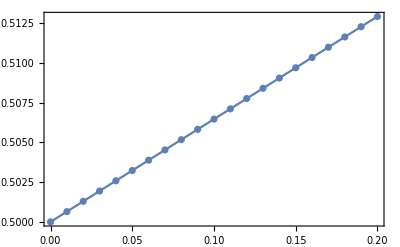

```mathematica
Show[ListPlot[aDat],Plot[aFit[γ],{γ,0,0.2}]]
```

```mathematica
bDat=ab[[;;,1;;3;;2]]
```

(0. | 0.333333
0.01 | 0.332259
0.02 | 0.331185
0.03 | 0.33011
0.04 | 0.329035
0.05 | 0.327959
0.06 | 0.326884
0.07 | 0.325808
0.08 | 0.324731
0.09 | 0.323655
0.1 | 0.322578
0.11 | 0.3215
0.12 | 0.320423
0.13 | 0.319345
0.14 | 0.318267
0.15 | 0.317188
0.16 | 0.316109
0.17 | 0.31503
0.18 | 0.31395
0.19 | 0.31287
0.2 | 0.31179)

```mathematica
bFit[γ_]=Fit[bDat, {1,γ,γ^2,γ^3},γ]
```

-0.0000199174 γ^3-0.00158525 γ^2-0.107397 γ+0.333333

### Export problem info to C

```mathematica
CForm[A//N]
```

List(List(-1.,0.),List(-1.,-2.))

```mathematica
CForm[Transpose[A//N]]
```

List(List(-1.,-1.),List(0.,-2.))

```mathematica
CForm[T//N]
```

List(List(List(0.05,0.1),List(0.15,0.2)),
   List(List(0.05,0.05),List(0.,0.15)))

```mathematica
CForm[b[t]]
```

List((40*Power(E,3*t)*t - 
      4*Power(0.3333333333333333 + t,2) - 
      5*Power(E,t)*(0.3333333333333333 + t)*
       (0.5 + Power(t,2)) - 
      Power(E,2*t)*Power(0.5 + Power(t,2),2))/
    (20.*Power(E,4*t)),
   (-4*Power(1 + 3*t,2) + 
      120*Power(E,3*t)*(1 + 2*Power(t,2)) - 
      2*Power(E,t)*(1 + 3*t)*(1 + 2*Power(t,2)) - 
      3*Power(E,2*t)*(-79 + 
         4*(Power(t,2) + Power(t,4))))/
    (240.*Power(E,4*t)))

```mathematica
CForm[SuperStar[x][γ,t]]
```

List((0.5 + Power(t,2))/Power(E,t) + (-0.5 + t)*t*γ,
   (0.3333333333333333 + t)/Power(E,2*t) + 
    ((-0.75 + t)*γ)/5.)

```mathematica
(* I think this is a left over from the analytical case CForm[Simplify[minSoln[γ]//N]]*)
```

List(0.49999999999999994 + 0.05503059750329588*γ,
   0.3333333333333333 - 0.1272325603758784*γ)

```mathematica
CForm[HornerForm[aFit[z]]] (* First component of arg min; i.e p^*[[1]]*)
```

0.5000000289639744 + z*
    (0.064717637614702 + 
      (-0.00044913462946438883 - 
         0.00001613396940867341*z)*z)

```mathematica
CForm[HornerForm[bFit[z]]] (* Second component of arg min; i.e p^*[[2]]*)
```

0.3333333245793077 + z*
    (-0.10739738478174649 + 
      (-0.0015852504354095308 - 
         0.000019917356023471516*z)*z)